```mathematica
vertex1 = RandomChoice[VertexList[g1]]
```

16

```mathematica
vertex2 = RandomChoice[VertexList[g2]]
```

11

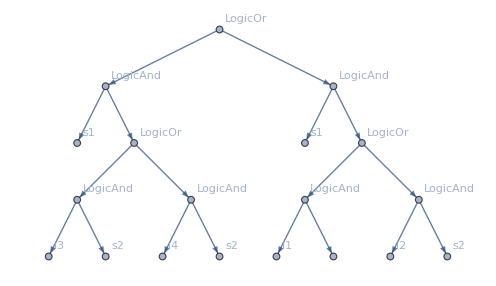
{-Graphics-,{1→Func[LogicOr],2→Func[LogicAnd],3→Term[s1],4→Func[LogicOr],5→Func[LogicAnd],6→Term[i3],7→Term[s2],8→Func[LogicAnd],9→Term[i4],10→Term[s2],11→Func[LogicAnd],12→Term[s1],13→Func[LogicOr],14→Func[LogicAnd],15→Term[i1],17→Func[LogicAnd],18→Term[i2],19→Term[s2]}}

```mathematica
cropped1 = DeleteSubtree[g1,l1,vertex1]
```

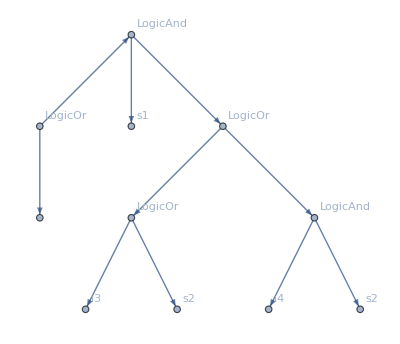
{-Graphics-,{1→Func[LogicOr],2→Func[LogicAnd],3→Term[s1],4→Func[LogicOr],5→Func[LogicOr],6→Term[i3],7→Term[s2],8→Func[LogicAnd],9→Term[i4],10→Term[s2]}}

```mathematica
cropped2 = DeleteSubtree[g2,l2,vertex2]
```

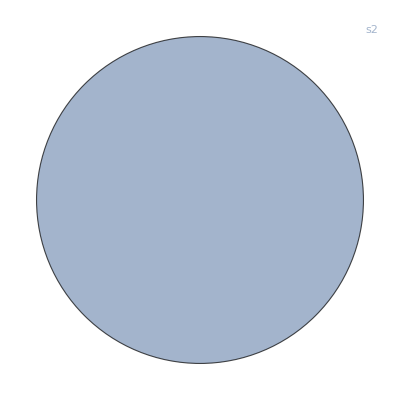
{-Graphics-,{16→Term[s2]}}

```mathematica
sub1 = Subtree[g1,l1,vertex1]
```

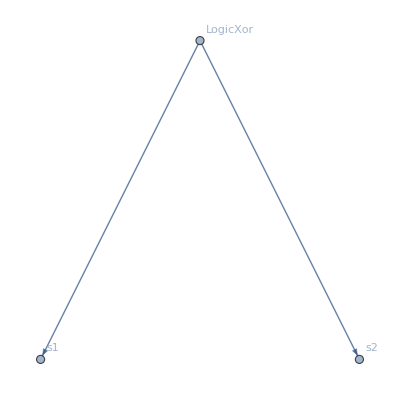
{-Graphics-,{11→Func[LogicXor],12→Term[s1],13→Term[s2]}}

```mathematica
sub2 = Subtree[g2,l2,vertex2]
```

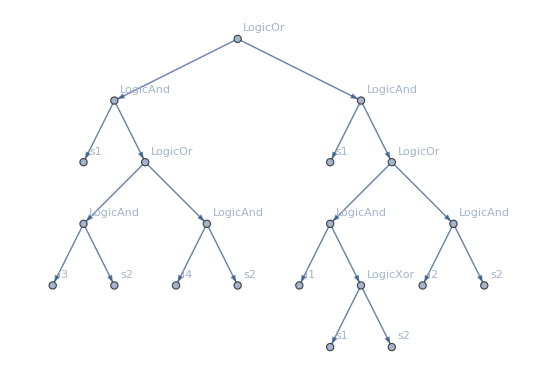
{-Graphics-,{1→Func[LogicOr],2→Func[LogicAnd],3→Term[s1],4→Func[LogicOr],5→Func[LogicAnd],6→Term[i3],7→Term[s2],8→Func[LogicAnd],9→Term[i4],10→Term[s2],11→Func[LogicAnd],12→Term[s1],13→Func[LogicOr],14→Func[LogicAnd],15→Term[i1],16→Func[LogicXor],17→Func[LogicAnd],18→Term[i2],19→Term[s2],20→Term[s1],21→Term[s2]}}

```mathematica
InsertSubtree[First[cropped1],Last[cropped1],First[sub2],Last[sub2],vertex2]
```